```mathematica
Apply
```

Table::write: Tag List in {i,1,6} is Protected.

Table[{i+j},{{i,1,6},{j,1,6}}]

```mathematica
f[x_,y_]:=x+y
```

```mathematica
6
```

```mathematica
Apply[f,CartesianProduct[{1,2,3,4,5,6},{1,2,3,4,5,6}]]
```

{2,4,6,8,10,12}

```mathematica
CartesianProduct[{1,2,3,4,5,6},{1,2,3,4,5,6}]
```

CartesianProduct[{1,2,3,4,5,6},{1,2,3,4,5,6}]

```mathematica
CartesianProduct[1,2]
```

CartesianProduct[1,2]

```mathematica
f[x_,y_]:=x+y
result=Apply[f,Table[{i,j},{i,1,6},{j,1,6}],{2}]
```

{{2,3,4,5,6,7},{3,4,5,6,7,8},{4,5,6,7,8,9},{5,6,7,8,9,10},{6,7,8,9,10,11},{7,8,9,10,11,12}}

```mathematica
Sum[i,{i,{Flatten@result}}]
```

{2,3,4,5,6,7,3,4,5,6,7,8,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12}

```mathematica
Flatten@result
```

{2,3,4,5,6,7,3,4,5,6,7,8,4,5,6,7,8,9,5,6,7,8,9,10,6,7,8,9,10,11,7,8,9,10,11,12}

```mathematica
Sum[1/i^2,{i,∞}](*wtttfffff?????????*)
```

π^2/6

```mathematica
Table[1/i,{i,1,20}]
```

```mathematica
{1,1/2,1/3,1/4,1/5,1/6,1/7,1/8,1/9,1/10,1/11,1/12,1/13,1/14,1/15,1/16,1/17,1/18,1/19,1/20,....,1/n}n->∞ =π^2/6 (*wtffffffoauishduoahduoashduoas/....=????????????????????*)
```

```mathematica
Sum[1/(2 i+1)^2,{i,-Infinity,Infinity}]
Table[1/(2i+1)^2,{i,-15,15}]
```

π^2/4

```mathematica
{1/n,1/841,1/729,1/625,1/529,1/441,1/361,1/289,1/225,1/169,1/121,1/81,1/49,1/25,1/9,1,1,1/9,1/25,1/49,1/81,1/121,1/169,1/225,1/289,1/361,1/441,1/529,1/625,1/729,1/841,1/961 1/(,n)}N->∞=π/4 (*???????????????AD?AD?AA?DA?DDA?AD?DA?AD?AD?ADAD?AD?AD?DA?AD?DA*)
```

```mathematica
{1/n,1/1521,1/1369,1/1225,1/1089,1/961,1/841,1/729,1/625,1/529,1/441,1/361,1/289,1/225,1/169,1/121,1/81,1/49,1/25,1/9,1,1,1/9,1/25,1/49,1/81,1/121,1/169,1/225,1/289,1/361,1/441,1/529,1/625,1/729,1/841,1/961,1/1089,1/1225,1/1369,1/1521,1/1681,1/n} N->∞=π/4
```

```mathematica
result=Apply[f,Table[{i,j},{i,1,6},{j,1,6}],{2}]
```

{{2,3,4,5,6,7},{3,4,5,6,7,8},{4,5,6,7,8,9},{5,6,7,8,9,10},{6,7,8,9,10,11},{7,8,9,10,11,12}}

```mathematica
TableForm[result]
TheSumOfTheNumbers=Total@Flatten@result
TheNumberOfNumbers=Length@Flatten@result
```

2 | 3 | 4 | 5 | 6 | 7
3 | 4 | 5 | 6 | 7 | 8
4 | 5 | 6 | 7 | 8 | 9
5 | 6 | 7 | 8 | 9 | 10
6 | 7 | 8 | 9 | 10 | 11
7 | 8 | 9 | 10 | 11 | 12

252

36

```mathematica
Total@Flatten@result
```

{27,33,39,45,51,57}

```mathematica
finalResult=(Total@Flatten@result)/(Length@Flatten@result):=(*Definition of the Expected Value; Expectation Value, Etc...AKA Average.*)
```

```mathematica
Length@Flatten@result
```

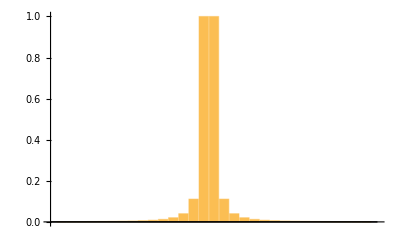

```mathematica
RectangleChart@Table[{1,1/(2i+1)^2},{i,-15,15}]
```

```mathematica
Manipulate[RectangleChart@Table[{1,1/(2i+1)^2},{i,-n,n}],{n,1,20}](*this is pending a write-up - this intriguing behavior where the rectangle-sizes approach eeach other right=to=left is quite serendipitious; it's honestly kind of troll....it's very arbitrary, it is likely because n  is going from left-to-right......Yep, played backward and it went left-to-right.

I don't like this....I'm not even interested in non-discrete values, and yet it's iterating over them, that's not ideal...I want integers only........
The list from n=0 must be a sort of series expansion for a particular function, more precisely, the series expansion for a particular INTEGRAL of a function (evaluated by Riemmann Sums)
	Whether this is true is unknown; whether it is, AND it's of some transformation of the exponential function is also unknown
)
```

```mathematica
Manipulate
```